```mathematica
Clear["Global`*"]
```

## GSF Fluxes

```mathematica
Get["/home/luca/repos/hyb_env_model/Mathematica/FluxInterpolation.wl"];
FluxInf[10.,0.]   (*6.15035e-5,flux to infinity,m1=1*)
FluxHor[10.,0.]   (*1.259e-8,horizon flux*)
fInf[rC,chi];fHor[rC,chi]   (*compactified r0^5 FI,r0^(15/2) FH (A13/A14)*)
rISCO[chi]   (*chi>0 prograde,chi<0 retrograde*)
(*FluxInf and FluxHor take the orbital radius r0 and the signed spin χ.They are valid for r0≥ISCO and|χ| ≤0.998. rISCO uses the closed-form formula,so you don't need to load KerrGeodesics.Each call takes about 27 µs.*)
```

0.0000615035

1.25913×10^-8

fHor[rC,chi]

rISCO[chi]

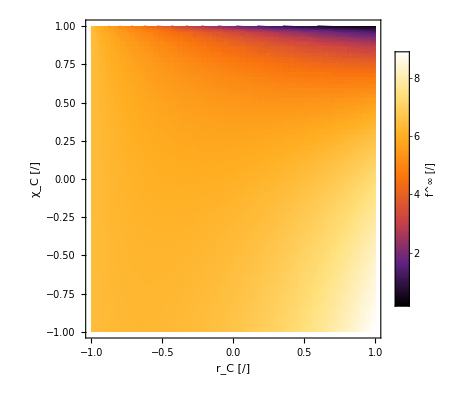

```mathematica
DensityPlot[fInf[rC,chi],{rC,-1,1},{chi,-1,1},PlotRange->All,PlotPoints->60,ColorFunction->"SunsetColors",MeshFunctions->{#3&},Mesh->20,MeshStyle->Directive[Black,Thin],Frame->True,AspectRatio->1,FrameLabel->{"\!\(\*SubscriptBox[\(r\), \(C\)]\) [/]","\!\(\*SubscriptBox[\(χ\), \(C\)]\) [/]"},PlotLegends->BarLegend[Automatic,LegendLabel->"\!\(\*SuperscriptBox[\(f\), \(∞\)]\) [/]"]]
```

## PN Data: Infinity Flux

## Nonspinning 4.5PN

```mathematica
(*Euler gamma:EulerGamma;lx stands for Log[x]*)
F0[nu_,lx_]:=1;

F1[nu_,lx_]:=-1247/336-(35/12) nu;

F15[nu_,lx_]:=4 Pi;

F2[nu_,lx_]:=-44711/9072+(9271/504) nu+(65/18) nu^2;

F25[nu_,lx_]:=(-8191/672-(583/24) nu) Pi;

F3[nu_,lx_]:=6643739519/69854400+(16/3) Pi^2-(1712/105) EulerGamma-(856/105) (Log[16]+lx)+(-134543/7776+(41/48) Pi^2) nu-(94403/3024) nu^2-(775/324) nu^3;

F35[nu_,lx_]:=(-16285/504+(214745/1728) nu+(193385/3024) nu^2) Pi;

F4[nu_,lx_]:=-323105549467/3178375200+(232597/4410) EulerGamma-(1369/126) Pi^2+(39931/294) Log[2]-(47385/1568) Log[3]+(232597/8820) lx+(-1452202403629/1466942400+(41478/245) EulerGamma-(267127/4608) Pi^2+(479062/2205) Log[2]+(47385/392) Log[3]+(20739/245) lx) nu+(1607125/6804-(3157/384) Pi^2) nu^2+(6875/504) nu^3+(5/6) nu^4;

F45[nu_,lx_]:=(265978667519/745113600-(6848/105) EulerGamma-(3424/105) (Log[16]+lx)+(2062241/22176+(41/12) Pi^2) nu-(133112905/290304) nu^2-(3719141/38016) nu^3) Pi;

(*Full flux,truncated at 4.5PN*)
FluxOrb[nu_,x_]:=(32 /5) nu^2 x^5*(F0[nu,Log[x]]+F1[nu,Log[x]]   x+F15[nu,Log[x]]  x^(3/2)+F2[nu,Log[x]]   x^2+F25[nu,Log[x]]  x^(5/2)+F3[nu,Log[x]]   x^3+F35[nu,Log[x]]  x^(7/2)+F4[nu,Log[x]]   x^4+F45[nu,Log[x]]  x^(9/2));
```

## Spin-Orbit 4PN

```mathematica
(*Spin-orbit flux coefficients.Sl=S_ell,Sigl=Sigma_ell,Dl=Delta (mass difference)*)
FSO0[nu_,Sl_,Dl_,Sigl_]:=-4 Sl-(5/4) Dl Sigl;

FSO1[nu_,Sl_,Dl_,Sigl_]:=(-9/2+(272/9) nu) Sl+(-13/16+(43/4) nu) Dl Sigl;

FSO15[nu_,Sl_,Dl_,Sigl_]:=-16 Pi Sl-(31 Pi/6) Dl Sigl;

FSO2[nu_,Sl_,Dl_,Sigl_]:=(476645/6804+(6172/189) nu-(2810/27) nu^2) Sl+(9535/336+(1849/126) nu-(1501/36) nu^2) Dl Sigl;

FSO25[nu_,Sl_,Dl_,Sigl_]:=(-3485 Pi/96+(13879 Pi/72) nu) Sl+(-7163 Pi/672+(130583 Pi/2016) nu) Dl Sigl;

(*Full spin-orbit flux,truncated at 2.5PN relative order*)
FluxSO[nu_,x_,M_,Sl_,Dl_,Sigl_]:=(32 nu^2 x^(13/2))/(5 M^2)*(FSO0[nu,Sl,Dl,Sigl]+FSO1[nu,Sl,Dl,Sigl]  x+FSO15[nu,Sl,Dl,Sigl] x^(3/2)+FSO2[nu,Sl,Dl,Sigl]  x^2+FSO25[nu,Sl,Dl,Sigl] x^(5/2));
```

## Spin-Spin 4PN

### Blanchet: 3PN

```mathematica
(*Spin-spin flux coefficients.Sl=S_ell,Sigl=Sigma_ell,Dl=Delta,kp=kappa_+,km=kappa_-*)
FSS0[nu_,Sl_,Dl_,Sigl_,kp_,km_]:=Sl^2 (2 kp+4)+Sl Sigl (2 Dl kp+4 Dl-2 km)+Sigl^2 ((-Dl km+kp+1/16)+nu (-2 kp-4));

FSS1[nu_,Sl_,Dl_,Sigl_,kp_,km_]:=Sl^2 ((41 Dl km/16-271 kp/112-5239/504)+nu (-43 kp/4-43/2))+Sl Sigl ((-279 Dl kp/56-817 Dl/56+279 km/56)+nu (-43 Dl kp/4-43 Dl/2+km/2))+Sigl^2 ((279 Dl km/112-279 kp/112-25/8)+nu (45 Dl km/16+243 kp/112+344/21)+nu^2 (43 kp/4+43/2));

(*Full SS flux,truncated at the order given*)
FluxSS[nu_,x_,m_,Sl_,Dl_,Sigl_,kp_,km_]:=(32 nu^2 x^7)/(5 m^4)*(FSS0[nu,Sl,Dl,Sigl,kp,km]+FSS1[nu,Sl,Dl,Sigl,kp,km] x);
```

```mathematica
Series[Coefficient[FluxSS[ν,x,m,S,Δ,Σ,2,0]/((32 /5) ν^2 *x^5)//Expand,x,3]//Expand,{ν,0,3}]//FullSimplify//Normal//Expand
```

-(3839 S^2)/(252 m^4)-(43 S^2 ν)/m^4-(1375 S Δ Σ)/(56 m^4)-(43 S Δ ν Σ)/m^4-(227 Σ^2)/(28 m^4)+(3481 ν Σ^2)/(168 m^4)+(43 ν^2 Σ^2)/m^4

### Cunningham+ 3.5PN

```mathematica
(*----------Flux:F_infty=(32 c^5 nu^2 x^5/(5G)) {...}----------*)

Fi0[nu_, lx_, s_, sg_, dl_] := 1;

Fi1[nu_, lx_, s_, sg_, dl_] := -1247/336 - 35/12 nu;

Fi15[nu_, lx_, s_, sg_, dl_] := 4 Pi - 4 s - 5/4 dl sg;

Fi2[nu_, lx_, s_, sg_, dl_] := -44711/9072 + 8 s^2 + 8 dl sg s + 
   33/16 sg^2 + nu (9271/504 - 8 sg^2) + 65/18 nu^2;

Fi25[nu_, lx_, s_, sg_, dl_] := -8191/672 Pi - 9/2 s - 13/16 dl sg + 
   nu (-583/24 Pi + 272/9 s + 43/4 dl sg);

Fi3[nu_, lx_, s_, sg_, dl_] := 
  6643739519/69854400 + 16/3 Pi^2 - 1712/105 EulerGamma - 
   856/105 (Log[16] + lx) - 16 Pi s - 31/6 Pi dl sg - 3839/252 s^2 - 
   1375/56 dl s sg - 227/28 sg^2 + 
   nu (-134543/7776 + 41/48 Pi^2 - 43 s^2 - 43 dl s sg + 
      3481/168 sg^2) + nu^2 (-94403/3024 + 43 sg^2) - 775/324 nu^3;

Fi35[nu_, lx_, s_, sg_, dl_] := -16285/504 Pi + 476645/6804 s + 
   9535/336 dl sg + 32 Pi s^2 + 32 Pi dl s sg + 65/8 Pi sg^2 - 
   16/3 s^3 + 2/3 dl s^2 sg + 9/2 s sg^2 + 35/24 dl sg^3 + 
   nu (214745/1728 Pi + 6172/189 s + 1849/126 dl sg - 32 Pi sg^2 - 
      56/3 s sg^2 - 6 dl sg^3) + 
   nu^2 (193385/3024 Pi - 2810/27 s - 1501/36 dl sg);

(* BUG: this definition adds a 7-argument rule to the package's FluxInf (same symbol), which is confusing. Renamed below.
FluxInf[nu_, x_, c_, G_, s_, sg_, 
   dl_] := (32 nu^2 x^5/5 )*(Fi0[nu, Log[x], s, sg, dl] + 
     Fi1[nu, Log[x], s, sg, dl]  x + 
     Fi15[nu, Log[x], s, sg, dl] x^(3/2) + 
     Fi2[nu, Log[x], s, sg, dl]  x^2 + 
     Fi25[nu, Log[x], s, sg, dl] x^(5/2) + 
     Fi3[nu, Log[x], s, sg, dl]  x^3 + 
     Fi35[nu, Log[x], s, sg, dl] x^(7/2));
*)
(* FIX: renamed to FluxInfCunningham *)
FluxInfCunningham[nu_, x_, c_, G_, s_, sg_, 
   dl_] := (32 nu^2 x^5/5 )*(Fi0[nu, Log[x], s, sg, dl] + 
     Fi1[nu, Log[x], s, sg, dl]  x + 
     Fi15[nu, Log[x], s, sg, dl] x^(3/2) + 
     Fi2[nu, Log[x], s, sg, dl]  x^2 + 
     Fi25[nu, Log[x], s, sg, dl] x^(5/2) + 
     Fi3[nu, Log[x], s, sg, dl]  x^3 + 
     Fi35[nu, Log[x], s, sg, dl] x^(7/2));
```

#### Compare the 3PN with Blanchet’s to match conventions

```mathematica
(*Blanchet, 3PN spin-spin term for spinless secondary around spinning primary*)
a=Table[Coefficient[Coefficient[FluxSS[ν,x,M,S,Δ,Σ,2,0]/((32 /5) ν^2 *x^5)//Expand,x,3]//Expand,ν,k],{k,0,2}]//MatrixForm

(*Cunningham, same but includes *)
b=Table[Coefficient[Fi3[ν,0,1/M^2 S,1/M^2 Σ,Δ]-Fi3[ν,0,0,0,0]//FullSimplify,ν,k],{k,0,2}]//Expand//MatrixForm

(*Make sure they match *)
a[[1]]-b[[1]]//FullSimplify
```

(-(3839 S^2)/(252 M^4)-(1375 S Δ Σ)/(56 M^4)-(227 Σ^2)/(28 M^4)
-(43 S^2)/M^4-(43 S Δ Σ)/M^4+(3481 Σ^2)/(168 M^4)
(43 Σ^2)/M^4)

(-(16 π S)/M^2-(3839 S^2)/(252 M^4)-(31 π Δ Σ)/(6 M^2)-(1375 S Δ Σ)/(56 M^4)-(227 Σ^2)/(28 M^4)
-(43 S^2)/M^4-(43 S Δ Σ)/M^4+(3481 Σ^2)/(168 M^4)
(43 Σ^2)/M^4)

{(π (96 S+31 Δ Σ))/(6 M^2),0,0}

### Cunningham 3.5 PNSS

```mathematica
Fi35Tot = Fi35[ν, Log[x], 1/M^2 S,1/M^2 Σ, Δ] // FullSimplify // Expand;
Fi35SS =Coefficient[Fi35Tot, S^2] - Coefficient[Coefficient[Fi35Tot, S^2], Σ] Σ -Coefficient[Coefficient[Fi35Tot, S^2], S] S;
Fi35ΣΣ =Coefficient[Fi35Tot, Σ^2] - Coefficient[Coefficient[Fi35Tot, Σ^2], S] S -Coefficient[Coefficient[Fi35Tot, Σ^2], Σ] Σ //FullSimplify;
Fi35SΣ =Coefficient[Fi35Tot, S*Σ] - Coefficient[Coefficient[Fi35Tot, S*Σ], S] S -Coefficient[Coefficient[Fi35Tot, S*Σ], Σ] Σ //FullSimplify;
F3p5SSblanchOLD[ν_, x_,M_,S_,Σ_, Δ_] = ((32 /5) ν^2 *x^5) FullSimplify[(Fi35SS S^2+Fi35ΣΣ Σ^2+ Fi35SΣ S Σ) x^( 7/2)];
F3p5SSblanchOLD[ν, x, M, S,Σ,Δ]

(* S WAY: take the part of Fi35 quadratic in the spins by rescaling S, Σ -> e S, e Σ and keeping the e^2 coefficient. New signature includes S and Σ. 
Definetly simpler but I like my dumb way better. It is nonetheless a good check that everything works 

F3p5SSblanch[ν_, x_, M_, S_, Σ_, Δ_] := Module[{e}, (32/5) ν^2 x^5 Coefficient[Expand[Fi35[ν, Log[x], e S/M^2, e Σ/M^2, Δ]], e, 2] x^(7/2)]
F3p5SSblanch[ν, x, M, S, Σ, Δ]
F3p5SSblanch[ν, x, M, 0, 0, Δ] (* check: must be 0 *)

F3p5SSblanch[ν, x, M, S, Σ, Δ]-F3p5SSblanchOLD[ν, x, M, Δ]//FullSimplify
*)
```

(4 π x^(17/2) ν^2 (256 S^2+256 S Δ Σ+(65-256 ν) Σ^2))/(5 M^4)

### Cho 4PN

```mathematica
F4SS[nu_, Sh_, Sigh_, dl_, kp_, 
   km_] := (-4289/648 - 295/21 nu + 54 nu^2 + 
      dl km (935/336 - 2153/144 nu) + 
      kp (-124577/9072 + 3265/126 nu + 
         27 nu^2)) Sh^2 + (km (74911/4536 - 52411/1008 nu + 
         1181/36 nu^2) + 
      dl (-160621/9072 + 9977/252 nu + 54 nu^2 + 
         kp (-74911/4536 + 41191/1008 nu + 27 nu^2))) Sh Sigh + (1633/
       336 + 465071/18144 nu - 74033/1008 nu^2 - 54 nu^3 + 
      dl km (74911/9072 - 46801/2016 nu + 209/144 nu^2) + 
      kp (-74911/9072 + 102979/2592 nu - 7109/168 nu^2 - 
         27 nu^3)) Sigh^2;

(* Contribution to the flux,including Newtonian prefactor *)
FluxSpin4[nu_, x_, Sh_, Sigh_, dl_, kp_, 
   km_] := (32 nu^2 x^5/(5)) F4SS[nu, Sh, Sigh, dl, kp, km] x^4;
```

```mathematica
FluxSpin4[ν,x,S/M^2,Σ/M^2,Δ,2,0]
```

32/5 x^9 ν^2 ((S^2 (-4289/648-(295 ν)/21+54 ν^2+2 (-124577/9072+(3265 ν)/126+27 ν^2)))/M^4+(S Δ (-160621/9072+(9977 ν)/252+54 ν^2+2 (-74911/4536+(41191 ν)/1008+27 ν^2)) Σ)/M^4+((1633/336+(465071 ν)/18144-(74033 ν^2)/1008-54 ν^3+2 (-74911/9072+(102979 ν)/2592-(7109 ν^2)/168-27 ν^3)) Σ^2)/M^4)

### Total

```mathematica
(* FIX: new F3p5SSblanch signature *)
FluxSSTot[ν_, x_, M_, S_, Δ_, Σ_, kp_, km_] := FluxSS[ν, x, M, S, Δ, Σ, 2, 0] + F3p5SSblanchOLD[ν, x, M, S, Σ, Δ] + FluxSpin4[ν, x, S/M^2, Σ/M^2, Δ, 2, 0]

((32 /5) ν^2 *x^5) (Collect[Expand[FluxSSTot[ν, x, M, S, Δ, Σ, 2,0]/((32 /5) ν^2 *x^5)], {x}, FullSimplify])
```

32/5 x^5 ν^2 ((π x^(7/2) (256 S^2+256 S Δ Σ+(65-256 ν) Σ^2))/(8 M^4)+(x^2 (128 S^2+128 S Δ Σ+(33-128 ν) Σ^2))/(16 M^4)+(x^3 (-2 S^2 (3839+10836 ν)-9 S Δ (1375+2408 ν) Σ+3 (-1362+ν (3481+7224 ν)) Σ^2))/(504 M^4)+(x^4 (32 S^2 (-19325+252 ν (85+243 ν))+2 S Δ (-460265+126 ν (8735+7776 ν)) Σ-(211462+ν (-1906777+126 ν (22763+15552 ν))) Σ^2))/(18144 M^4))

## Spin-Spin-Spin 4PN

```mathematica
(*Spin-cubed flux coefficient.Sh=S_ell,Sigh=Sigma_ell,dl=delta,kp=kappa_+,km=kappa_-,lp=lambda_+,lm=lambda_-*)
fSSS3[nu_,Sh_,Sigh_,dl_,kp_,km_,lp_,lm_]:=Sh^3 (-16 kp/3-4 lp+40/3);

fSSS2[nu_,Sh_,Sigh_,dl_,kp_,km_,lp_,lm_]:=Sh^2 Sigh (dl (-35 kp/6-6 lp+73/3)-3 km/4+6 lm);

fSSS1[nu_,Sh_,Sigh_,dl_,kp_,km_,lp_,lm_]:=Sh Sigh^2 (-35 dl km/12+6 dl lm+35 kp/12-6 lp+32/3+nu (22 kp/3+12 lp-172/3));

fSSS0[nu_,Sh_,Sigh_,dl_,kp_,km_,lp_,lm_]:=Sigh^3 (67 dl kp/24-2 dl lp-dl/8-67 km/24+2 lm+nu (dl kp/2+2 dl lp-11 dl+61 km/12-6 lm));

(*Full SSS coefficient*)
fSSS[nu_,Sh_,Sigh_,dl_,kp_,km_,lp_,lm_]:=fSSS3[nu,Sh,Sigh,dl,kp,km,lp,lm]+fSSS2[nu,Sh,Sigh,dl,kp,km,lp,lm]+fSSS1[nu,Sh,Sigh,dl,kp,km,lp,lm]+fSSS0[nu,Sh,Sigh,dl,kp,km,lp,lm]

(*Contribution to the flux,assuming the standard prefactor and x^(7/2)*)
FluxSSS[nu_,x_,M_,Sh_,Sigh_,dl_,kp_,km_,lp_,lm_]:=(32nu^2 x^5/(5 M^6)) fSSS[nu,Sh,Sigh,dl,kp,km,lp,lm] x^(7/2)
```

## Full PN Flux @ Infty

```mathematica
FullInfFluxPN[x_,ν_,M_,S_,Σ_,Δ_]:=Collect[Expand[(1/(32/5 ν^2 x^5))(FluxOrb[ν,x]+FluxSO[ν,x,M,S,Δ,Σ]+FluxSSTot[ν,x,M,S,Δ,Σ,2,0]+FluxSSS[ν,x,M,S,Σ,Δ,2,0,2,0])],{x,ν}]
FullInfFluxPNSFvars[x_,ν_,M_,χ_]=32/5 ν^2 x^5 Collect[FullInfFluxPN[x,ν,M,M^2/4(1+√(1-4ν))^2 χ,-M^2/2(1+√(1-4ν))χ,√(1-4ν)],x,FullSimplify]
```

32/5 x^5 ν^2 (1+1/336 x (-1247-980 ν)+x^(3/2) (4 π-11/8 (1+√(1-4 ν)) χ+(3 ν χ)/2)+(x^(5/2) (-3 π (8191+16324 ν)+7 (-531 (1+√(1-4 ν))+4 (908+701 √(1-4 ν)-628 ν) ν) χ))/2016+(x^2 (-89422+18711 (1+√(1-4 ν)) χ^2+18 ν (18542+3640 ν-2079 χ^2)))/18144+(x^(7/2) (45 π (-78168+9828 (1+√(1-4 ν)) χ^2+ν (300643+154708 ν-19656 χ^2))+2 χ (1125936 ν^3-36 ν^2 (52159+47159 √(1-4 ν)+6678 χ^2)-7 (1+√(1-4 ν)) (-162035+11502 χ^2)+ν (-234436+489384 √(1-4 ν)+1134 (319+177 √(1-4 ν)) χ^2))))/108864+x^(9/2) ((41 π^3 ν)/12-(π (-797936002557+145786798080 EulerGamma+700 ν (-296962704+ν (1464241955+312407844 ν))+72893399040 Log[16]))/2235340800-3424/105 π Log[x])+x^4 ((-1938633296802-18878631247177 ν)/19070251200+(EulerGamma (232597+746604 ν))/4410+(39931 Log[2])/294-(47385 Log[3])/1568+1/30481920(-945 π^2 (350464+49 ν (38161+5412 ν))+7560 π (-51696 (1+√(1-4 ν))+(318443+258029 √(1-4 ν)-254892 ν) ν) χ+8 (9520140 (1+√(1-4 ν)) χ^2+ν (-105 (1315129+1133793 √(1-4 ν)) χ^2+70 ν (12857000+189 (31968+18767 √(1-4 ν)) χ^2+54 ν (13750+840 ν-47159 χ^2))+216 (3832496 Log[2]+2132325 Log[3]))))+((232597+746604 ν) Log[x])/8820)+x^3 (6643739519/69854400-(1712 EulerGamma)/105+1/48 π^2 (256+41 ν)-1/12 π (65 (1+√(1-4 ν))-68 ν) χ+(611 (1+√(1-4 ν)) χ^2)/1008-(ν (941801+108 (6274+5663 √(1-4 ν)) χ^2+6 ν (283209+21700 ν-119322 χ^2)))/54432-856/105 Log[16 x]))

## Hybrid Flux @ Infty

```mathematica
(* BUG: r0 = 1/x is the Schwarzschild relation only. Honet sets m1 Ω = x^(3/2), so r0 = (x^(-3/2) - χ)^(2/3), and the normalization must be 32/5 x^5, not 32/5 r0^-5 (eq. A15).
Of course you need to use rhe Kepler radius, not the coordinate radius.. dumb me
Needs["KerrGeodesics`"];
FluxHorSF[x_, χ_] := 
 5/32 fInf[2 KerrGeoISCO[χ, 1] x - 1, χ]
*)
(* FIX: eq. A15 with Ω-hat = x^(3/2), via the package FluxInf[r0, χ] (no KerrGeodesics needed). *)
FluxInfSF[x_, χ_] := FluxInf[(x^(-3/2) - χ)^(2/3), χ]

FhatInfPN[x_,ν_,M_,χ_]=(1/(32/5 ν^2 x^5))FullInfFluxPNSFvars[x,ν,M,χ];
FhatInfSF[x_,χ_]=(1/(32/5 x^5))FluxInfSF[x,χ];
```

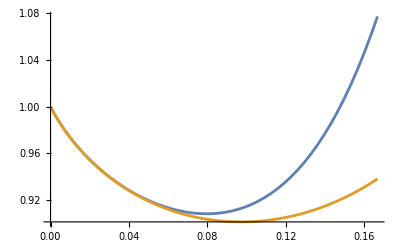

```mathematica
spin = 0.5;
Plot[
 {
  FhatInfPN[x, 0, 1, spin],
  FhatInfSF[x, spin]
  },
 {x, 0, 1/6}
 ]
```

```mathematica
HybridInfFluxNewtNorm[x_,ν_,χ_]:=FhatInfSF[x,χ]+FhatInfPN[x,ν,1,χ]-FhatInfPN[x,0,1,χ]
HybridInfFlux[x_,ν_,χ_]:=(32/5 ν^2 x^5)HybridInfFluxNewtNorm[x,ν,χ]
```

```mathematica
(* NEW: check in the test-mass limit. SF minus PN(ν->0) must be small and fall off like x^4 (unknown 4PN SSS, spin^4) or x^5 (5PN). An error at <= 3.5PN would fall off more slowly. *)
TableForm[Table[FhatInfSF[x0, chi0] - FhatInfPN[x0, 0, 1, chi0], {x0, {0.02, 0.04, 0.06, 0.1}}, {chi0, {-0.5, 0., 0.5}}], TableHeadings -> {{0.02, 0.04, 0.06, 0.1}, {"χ=-0.5", "χ=0", "χ=0.5"}}]
```

| χ=-0.5 | χ=0 | χ=0.5
0.02 | 0.00002539 | -7.41508×10^-6 | -0.0000536158
0.04 | 2.97865×10^-6 | -0.000125921 | -0.000263521
0.06 | -0.000281902 | -0.000869238 | -0.00132876
0.1 | -0.00341568 | -0.0096634 | -0.0132506

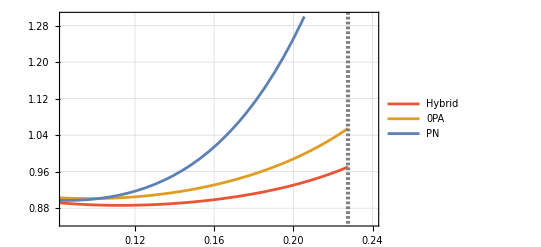

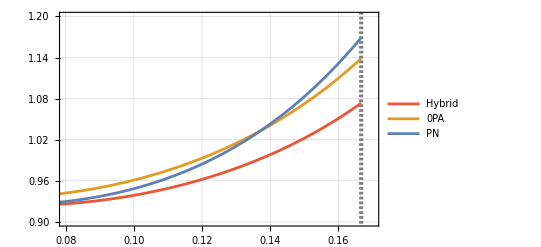

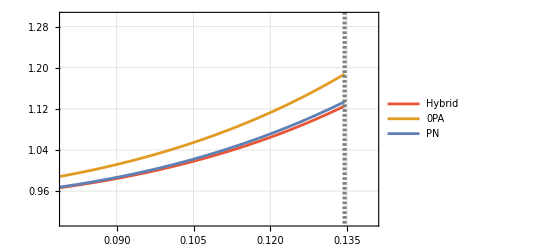

```mathematica
blue=ColorData[97][1];  (*RGBColor[0.368417,0.506779,0.709798]—PN*)
orange=ColorData[97][2];  (*RGBColor[0.880722,0.611041,0.142051]—0PA*)
red=RGBColor[234/255,85/255,54/255]; (*RGBColor[0.922526,0.385626,0.209179]—Hybrid*)

xISCO[χ_] := (rISCO[χ]^(3/2) + χ)^(-2/3);
q = 14;
a = 0.5;
Plot[{
HybridInfFluxNewtNorm[x, q/(1 + q)^2,  a], 
FhatInfSF[x, a], 
FhatInfPN[x, q/(1 + q)^2, 1, a]
}, 
{x, 0, xISCO[a]}, 
GridLines -> Automatic,
 Frame -> True, 
PlotRange -> {{0.085, 0.24}, {0.85, 1.3}},
PlotStyle->{red,orange,blue,},
PlotLegends->{"Hybrid","0PA","PN"},
Epilog->{{
GrayLevel[0.5],
AbsoluteThickness[3],
AbsoluteDashing[{2,1.5}],
InfiniteLine[{ xISCO[a],0},{0,1}]
}}
]

a = 0;
Plot[{
HybridInfFluxNewtNorm[x, q/(1 + q)^2,  a], 
FhatInfSF[x, a], 
FhatInfPN[x, q/(1 + q)^2, 1, a]
}, 
 {x, 0, xISCO[a]}, 
GridLines -> Automatic, 
Frame -> True, 
PlotRange -> {{0.08, 0.17}, {0.9, 1.2}},
PlotStyle->{red,orange,blue},
PlotLegends->{"Hybrid","0PA","PN"},
Epilog->{{
GrayLevel[0.5],
AbsoluteThickness[3],
AbsoluteDashing[{2,1.5}],
InfiniteLine[{ xISCO[a],0},{0,1}]
}}
]

a = -0.5;
Plot[{
HybridInfFluxNewtNorm[x, q/(1 + q)^2,  a], 
FhatInfSF[x, a], 
FhatInfPN[x, q/(1 + q)^2, 1, a]
}, 
 {x, 0, xISCO[a]}, 
GridLines -> Automatic, 
Frame -> True, 
PlotRange -> {{0.08, 0.14}, {0.9, 1.3}},
PlotStyle->{red,orange,blue},
PlotLegends->{"Hybrid","0PA","PN"},
Epilog->{{
GrayLevel[0.5],
AbsoluteThickness[3],
AbsoluteDashing[{2,1.5}],
InfiniteLine[{ xISCO[a],0},{0,1}]
}}
]
```

## PN Data: Horizon Flux

## Saketh+ 4PN orbital and 2.5PN spin

```mathematica
(*k=√(1-χ^2) and B(χ)=Im[PolyGamma[0,3+2 iχ/κ]*)

Cx0[X1_,chi1_,chi2_,k1_,B2_]:=1+3 chi1^2;

Cx2[X1_,chi1_,chi2_,k1_,B2_]:=(1/4) (3 (2+chi1^2)+2 X1 (1+3 chi1^2) (2+3 X1));

Cx3[X1_,chi1_,chi2_,k1_,B2_]:=(1/2) (-4+3 chi1^2) chi2-2 X1 (1+3 chi1^2) (X1 (chi1+chi2)+4 B2)+X1 (-(2/3) (23+30 k1) chi1+(7-12 k1) chi1^3+4 chi2+(9/2) chi1^2 chi2);

(*Full C_x; the x^12 is part of the prefactor*)
Cx[M_,X1_,eta_,x_,chi1_,chi2_,k1_,B2_]:=-(16/5) M^2 X1^2 eta^2 (1+k1) x^6*(Cx0[X1,chi1,chi2,k1,B2]+Cx2[X1,chi1,chi2,k1,B2] x+Cx3[X1,chi1,chi2,k1,B2] x^(3/2));

dm1dt[Om_,OmH_,M_,X1_,eta_,x_,chi1_,chi2_,k1_,B2_]:=Om (OmH-Om) Cx[M,X1,eta,x,chi1,chi2,k1,B2];
```

```mathematica
m1[M_,ν_]:=M/2(1+√(1-4ν))
kappa[χ_]:=√(1-χ^2)
B2[χ_]:=Im[PolyGamma[0,3+2 I χ/kappa[χ]]]
OmgH[χ_,M_,ν_]:=χ/(2 m1[M,ν](1+kappa[χ]))
OmgTidal[x_,M_,ν_,χ_]:=x^(3/2)/M(1-ν x + ν χ x^(3/2))
```

```mathematica
FullHorizonFluxPN[x_,ν_,M_,χ_]=dm1dt[OmgTidal[x,M,ν,χ],OmgH[χ,M,ν],1,m1[M,ν]/M,ν,x,χ,0,kappa[χ],B2[χ]]
```

-1/(5 M)4 x^(15/2) (1+√(1-4 ν))^2 ν^2 (1-x ν+x^(3/2) ν χ) (1+√(1-χ^2)) (-(x^(3/2) (1-x ν+x^(3/2) ν χ))/M+χ/(M (1+√(1-4 ν)) (1+√(1-χ^2)))) (1+3 χ^2+1/4 x (3 (2+χ^2)+(2+3/2 (1+√(1-4 ν))) (1+√(1-4 ν)) (1+3 χ^2))+x^(3/2) (1/2 (1+√(1-4 ν)) (χ^3 (7-12 √(1-χ^2))-2/3 χ (23+30 √(1-χ^2)))-(1+√(1-4 ν)) (1+3 χ^2) (1/2 (1+√(1-4 ν)) χ+4 Im[PolyGamma[0,3+(2 ⅈ χ)/(√(1-χ^2))]])))

```mathematica
(*Collect[FullHorizonFlux[x,ν,χ]/(-(16/5)m1[1,ν]^2 ν^2 (1+kappa[χ]) x^12),{x,ν},FullSimplify]*)
```

```mathematica
(*CompletePNFlux[x_,ν_,M_,χ_]:=FullInfFluxPN[x,ν,M,χ]+FullHorizonFluxPN[x,ν,M,χ]*)
```

```mathematica
Series[FullHorizonFluxPN[x,ν,1,χ],{ν,0,2}]//Normal//Simplify
SeriesCoefficient[FullHorizonFluxPN[x,ν,1,χ],{ν,0,2}]//Simplify
FullHorizonFluxPN[x,ν,1,χ]/ν^2//Simplify
```

-2/15 x^(15/2) ν^2 (-χ+2 x^(3/2) (1+√(1-χ^2))) (-12 (1+3 χ^2)-3 x (16+33 χ^2)+4 x^(3/2) χ (52+60 √(1-χ^2)+χ^2 (-3+36 √(1-χ^2)))+96 x^(3/2) (1+3 χ^2) Im[PolyGamma[0,3+(2 ⅈ χ)/(√(1-χ^2))]])

-2/15 x^(15/2) (-χ+2 x^(3/2) (1+√(1-χ^2))) (-12 (1+3 χ^2)-3 x (16+33 χ^2)+4 x^(3/2) χ (52+60 √(1-χ^2)+χ^2 (-3+36 √(1-χ^2)))+96 x^(3/2) (1+3 χ^2) Im[PolyGamma[0,3+(2 ⅈ χ)/(√(1-χ^2))]])

-4/5 x^(15/2) (1+√(1-4 ν))^2 (1-x ν+x^(3/2) ν χ) (1+√(1-χ^2)) (x^(3/2) (-1+x ν-x^(3/2) ν χ)+χ/((1+√(1-4 ν)) (1+√(1-χ^2)))) (1+3 χ^2+1/4 x (11+5 √(1-4 ν)+3 (6+5 √(1-4 ν)) χ^2-6 ν (1+3 χ^2))-1/6 x^(3/2) (1+√(1-4 ν)) (χ (49+3 √(1-4 ν)+60 √(1-χ^2)+3 χ^2 (-4+3 √(1-4 ν)+12 √(1-χ^2)))+24 (1+3 χ^2) Im[PolyGamma[0,3+(2 ⅈ χ)/(√(1-χ^2))]]))

```mathematica
FluxHorSF[x_, χ_] := FluxHor[(x^(-3/2) - χ)^(2/3), χ]
```

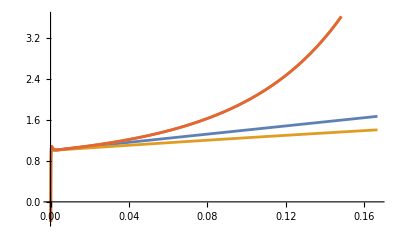

```mathematica
HybridHorFlux[x_,ν_,χ_]:=ν^2(FluxHorSF[x,χ]+Simplify[FullHorizonFluxPN[x,ν,1,χ]/ν^2]-Simplify[SeriesCoefficient[FullHorizonFluxPN[x,ν,1,χ],{ν,0,2}]])
FhatHorFluxPN[x_,ν_,M_,χ_]=Simplify[FullHorizonFluxPN[x,ν,M,χ]/(((1+kappa[χ])*m1[M,ν]^2*16 ν^2 x^9)/5)];
Plot[{
(*Simplify[FullHorizonFluxPN[x,ν,1,0]/((2*16 ν^2 x^9)/5)]/.ν->0,
FullHorizonFluxPN[x,0.05,1,0]/((2*16 ν^2 x^9)/5),
*)
Limit[FhatHorFluxPN[x,ν,1,0],ν->0],
Limit[FhatHorFluxPN[x,ν,1,0],ν->0.2],
FluxHorSF[x,0]/((2*16 x^9)/5),
Limit[HybridHorFlux[x,ν,0]/((2*16 ν^2 x^9)/5),ν->0]
},
{x,0,1/6}(*,
PlotRange->{{0,0.01},Automatic}*)
]
```

```mathematica
Series[HybridHorFlux[x,ν,0]/((2*16 ν^2 x^9)/5),{ν,0,6}]
```

(5 FluxHor[(1/x^(3/2))^(2/3),0])/(32 x^9)-2 (1+7 x+4 x^2) ν+1/2 (-2+11 x+50 x^2+8 x^3) ν^2+1/16 (64 x-8 (4+16 x)+x^2 (-64 x-8 (4+16 x))-2 x (88 x-4 (4+16 x))) ν^3+1/16 (128 x-20 (4+16 x)-2 x (64 x-8 (4+16 x))+x^2 (88 x-4 (4+16 x))) ν^4+1/16 (320 x-56 (4+16 x)-2 x (128 x-20 (4+16 x))+x^2 (64 x-8 (4+16 x))) ν^5+1/16 (896 x-168 (4+16 x)-2 x (320 x-56 (4+16 x))+x^2 (128 x-20 (4+16 x))) ν^6+O[ν]^7

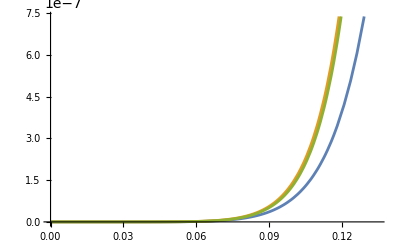

```mathematica
chi=-0.5;
q=14;
Plot[{
Limit[FullHorizonFluxPN[x,ν,1,chi]/ν^2,ν-> q/(1 + q)^2],
FluxHorSF[x,chi],
Limit[HybridHorFlux[x,ν,chi]/ν^2,ν-> q/(1 + q)^2]
},
{x,0,xISCO[chi]}(*,
PlotRange->{{0,0.01},Automatic}*)
]
```